# 2021-11-11

## Ex

Bestäm eventuella lokala extrempunkter och terasspunkter till f(x)=2arctan(x)-x^3/(x^2+1) samt eventuella asymptoter till kurvan y = f(x).

```mathematica
Remove["Global`*"]
```

```mathematica
f[x_]:=2ArcTan[x]-x^3/(x^2+1)
```

```mathematica
{Limit[f[x],x->-∞],Limit[f[x],x->∞]}
```

```mathematica
{k=Limit[f[x]/x,x->-∞],m=Limit[f[x]-k x,x->-∞]}
```

```mathematica
y1=k x+m
```

```mathematica
{k=Limit[f[x]/x,x->∞],m=Limit[f[x]-k x,x->∞]}
```

```mathematica
y2=k x+m
```

```mathematica
Plot[{f[x],y1,y2},{x,-10,10}]
```

```mathematica
P1=Plot[f[x],{x,-10,10},PlotStyle->{Orange }];
P2=Plot[y1,{x,-10,-5},PlotStyle->{Green }];
P3=Plot[y2,{x,3,10},PlotStyle->{Blue}];
```

```mathematica
Show[P1,P2,P3]
```

```mathematica
Plot[{f[x],f'[x]},{x,-10,10},PlotStyle->{Blue,Green}]
```

```mathematica
der=Solve[f'[x]==0,Reals]
```

```mathematica
punkter={x,f[x]}/.der
```

```mathematica
Plot[{f[x],f'[x]},{x,-10,10},Epilog->{Red,PointSize[0.015],Point[punkter]}]
```

## Ex

På höjden 20 m över marken sitter en gatlampa. En mörk kväll släpper Boll-Kalle en liten
boll från samma höjd men 10 m från lampan. Med vilken hastighet rör sig bollens skugga på
marken
i. 1 s efter att bollen släppts?
ii. precis innan bollen träffar marken?

```mathematica
Remove["Global`*"]
```

```mathematica
ekv=y/x==20/(10+x);
```

```mathematica
Dt[ekv,t]
```

```mathematica
xprim=Solve[{ekv,Dt[ekv,t]},{x,Dt[x,t]}]//First
```

```mathematica
Dt[x,t]/.xprim/.Dt[y,t]->-g t/.y->-g t^2/2+20/.t->1/.g->10
```

```mathematica
Solve[-g t^2/2+20==0,t]/.g->10
```

```mathematica
Dt[x,t]/.xprim/.Dt[y,t]->-g t/.y->-g t^2/2+20/.t->2/.g->10
```

### alternativt

```mathematica
Remove["Global`*"]
```

```mathematica
ekv=y[t]/x[t]==20/(10+x[t]);
```

```mathematica
D[ekv,t]
```

```mathematica
xprim=Solve[{ekv,D[ekv,t]},{x'[t],x[t]}]//First
```

```mathematica
x'[t]/.xprim/.y'[t]->-g t/.y[t]->-g t^2/2+20/.t->1/.g->10
```

```mathematica
Solve[-g t^2/2+20==0,t]/.g->10
```

```mathematica
x'[t]/.xprim/.y'[t]->-g t/.y[t]->-g t^2/2+20/.t->2/.g->10
```

## Ex

En 10 m lång stege lutar mot ett 3 m högt staket. Botten av stegen dras bort från staketet
med farten 1.5 m/s. Med vilken fart rör sig toppen av stegen i
i. vertikal riktning
ii. horisontell riktning
då avståndet mellan staketet och stegens botten är 4 m?

-Graphics-

```mathematica
Remove["Global`*"]
```

```mathematica
ekv={(a[t]+x[t])^2+y[t]^2==10^2,y[t]/(a[t]+x[t])==3/x[t]}
```

```mathematica
D[ekv,t]
```

```mathematica
sys=Join[ekv,D[ekv,t]]
```

```mathematica
lösn=Solve[sys,{y[t],a[t],y'[t],a'[t]}];
```

```mathematica
svar={y[t],y'[t],a[t],a'[t]}/.lösn/.x[t]->4/.x'[t]->3/2//Last
```

-Graphics-

```mathematica
Remove["Global`*"]
```

```mathematica
ekv={(a+x)^2+y^2==10^2,y/(a+x)==3/x}
```

```mathematica
sys=Join[ekv,Dt[ekv,t]]
```

```mathematica
lösn=Solve[sys,{y,a,Dt[y,t],Dt[a,t]}];
```

```mathematica
svar={y,Dt[y,t],a,Dt[a,t]}/.lösn/.Dt[x,t]->3/2/.x->4//Last
```

## Ex

Bestäm den punkt på kurvan y=1-x^2 där tangenten till kurvan skär ut den minsta möjliga
triangeln ur första kvadranten.

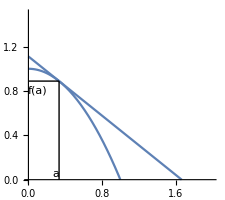

```mathematica
Remove["Global`*"]
```

y-y_0=k(x-x_0)
y=k(x-x_0)+y_0
y=f'(a)(x-a)+f(a)

```mathematica
f[x_]:=1-x^2
g[x_]:=f'[a](x-a)+f[a]
```

```mathematica
bas=x/.Solve[g[x]==0]//First;
höjd=g[0];
```

Triangelarea

```mathematica
Subscript[A, tri]=1/2 höjd*bas
```

```mathematica
Plot[Subscript[A, tri],{a,0,1}]
```

Minsta area

```mathematica
Solve[D[Subscript[A, tri],a]==0.]//Last
```

```mathematica
g[x]
```

```mathematica
Manipulate[Plot[{f[x],-a^2-2 a (x-a)+1},{x,0,2},AspectRatio->Automatic,PlotRange->{{0,2},{0,2}}],{a,0.1,1}]
```

### Extra

```mathematica
Manipulate[Plot[Sin[x+c],{x,-2π,2π},AspectRatio->Automatic,PlotRange->{{-2π,2π},{-2,2}}],{c,-π,π}]
```

```mathematica
Manipulate[Plot[a Sin[b x+c]+d,{x,-2π,2π},AspectRatio->Automatic,PlotRange->{{-2π,2π},{-5,5}}],{a,0,3},{b,0,2},{c,-π,π},{d,-1,1}]
```

```mathematica
(*Plot[{f[x],-a^2-2 a (x-a)+1}/.a->1/3,{x,0,2},AspectRatio->Automatic,PlotRange->{{0,2},{0,3/2}},Ticks->None,Epilog->{Line[{{1/3,0},{1/3,f[1/3]}}],Line[{{0,f[1/3]},{1/3,f[1/3]}}],Text["a",{0.3,0.05}],Text["f(a)",{0.1,0.8}]}]*)
```

## Ex

Bestäm y' i punkten (1,2) då 4x y^2-12x y+13=5x

```mathematica
Remove["Global`*"]
ekv=Dt[4x y^2-12x y+13==5x,x]
```

```mathematica
dydx=Solve[ekv,Dt[y,x]]
```

Vad händer nu om jag stoppar in punkten?

```mathematica
dydx/.{x->1,y->2}
```

Hur fixar man detta?

```mathematica
dydx/.Dt[y,x]->🐺
```

```mathematica
dydx/.Dt[y,x]->🐺/.{x->1,y->2}
```

```mathematica
dydx/.Dt[y,x]->🐺/.{x->1,y->2}/.🐺->Dt[y,x]
```

Eller lite mer tekniskt

```mathematica
:>
```

```mathematica
dydx/.Rule[a_,b_]:>Rule[a,b/.{x->1,y->2}]
```

## Ex

En räv promenerar längs stigen x+y^3=1. Sök ẏ då x=0,y=1 och ẋ=4

```mathematica
Remove["Global`*"]
```

```mathematica
ContourPlot[{x+y^3==1},{x,0,3/2},{y,0,3/2},Epilog->Text["🐺",{0.6,0.8}]]
```

```mathematica
dydt=Solve[Dt[x+y^3==1,t],Dt[y,t]]
```

```mathematica
dydt/.{Dt[x,t]->4,y->1,x->0}
```

Hur fixade vi detta???

```mathematica
dydt/.{Dt[y,t]->räv,Dt[x,t]->4,y->1,x->0}/.räv->Dt[y,t]
```

Eller

```mathematica
dydt/.Rule[a_,b_]:>Rule[a,b/.{Dt[x,t]->4,y->1,x->0}]
```

## Extra

```mathematica
Remove["Global`*"]
```

```mathematica
Manipulate[Plot[a x^3+b x^2+c x+d,{x,-2π,2π},AspectRatio->Automatic,PlotRange->{{-2π,2π},{-5,5}}],{a,-5,5},{b,-5,5},{c,-5,5},{d,-5,5}]
```

```mathematica
Manipulate[Plot3D[Cos[Sin[a x+b y]],{x,-2π,2π},{y,-2π,2π},AspectRatio->Automatic,PlotRange->{{-2π,2π},{-5,5}}],{a,0,2π},{b,0,2π}]
```